```mathematica
ClearAll["Global`*"];
```

```mathematica
unitFrequency =2 Pi 299792458/(137×5.29177210903×10^-11);   (*Conversion factor for frequency from SI to atomic unit*)
ScalarShift[d_,ω_,δω_]:=d^2×δω/(δω^2-ω^2);   (*Reduced Matrix Element and Frequency Part of scalar light shift*)
VectorShift[d_,ω_,δω_]:=d^2×ω/(δω^2-ω^2);(*Reduced Matrix Element and Frequency Part of vector light shift*)
P612s = ScalarShift[4.489,ω,8.103940130821×10^-3]; (* scalar shift from 6P1/2*)
P612v = VectorShift[4.489,ω,8.103940130821×10^-3]; (* vector shift from 6P1/2*)
P632s = ScalarShift[6.324,ω,8.505603284712×10^-3]; (* scalar shift from 6P3/2*)
P632v = VectorShift[6.324,ω,8.505603284712×10^-3];  (* vector shift from 6P3/2*)
P712s = ScalarShift[0.276,ω,1.577928482430×10^-2]; 
P712v = VectorShift[0.276,ω,1.577928482430×10^-2];
P732s = ScalarShift[0.586,ω,1.591054042095×10^-2];
P732v = VectorShift[0.586,ω,1.591054042095×10^-2];
P812s = ScalarShift[0.081,ω,1.863820590141×10^-2]; 
P812v = VectorShift[0.081,ω,1.863820590141×10^-2]; 
P832s = ScalarShift[0.218,ω,1.869814122798×10^-2];
P832v = VectorShift[0.218,ω,1.869814122798×10^-2];
P912s = ScalarShift[0.043,ω,2.003607022684×10^-2]; 
P912v = VectorShift[0.043,ω,2.003607022684×10^-2]; 
P932s = ScalarShift[0.127,ω,2.006846317056×10^-2];
P932v = VectorShift[0.127,ω,2.006846317056×10^-2];
P1012s = ScalarShift[0.047,ω,2.082615694340×10^-2]; 
P1012v = VectorShift[0.047,ω,2.082615694340×10^-2]; 
P1032s = ScalarShift[0.114,ω,2.084563304712×10^-2];
P1032v = VectorShift[0.114,ω,2.084563304712×10^-2];
P1112s = ScalarShift[0.034,ω,2.131668135535×10^-2]; 
P1112v = VectorShift[0.034,ω,2.131668135535×10^-2]; 
P1132s = ScalarShift[0.085,ω,2.132929653417×10^-2];
P1132v = VectorShift[0.085,ω,2.132929653417×10^-2];
P1212s = ScalarShift[0.026,ω,2.164220024461×10^-2]; 
P1212v = VectorShift[0.026,ω,2.164220024461×10^-2]; 
P1232s = ScalarShift[0.067,ω,2.165083718607×10^-2];
P1232v = VectorShift[0.067,ω,2.165083718607×10^-2];
P1312s = ScalarShift[0.021,ω,2.186928834723×10^-2]; 
P1312v = VectorShift[0.021,ω,2.186928834723×10^-2]; 
P1332s = ScalarShift[0.055,ω,2.187545767708×10^-2];
P1332v = VectorShift[0.055,ω,2.187545767708×10^-2];
P1412s = ScalarShift[0.017,ω,2.203400475076×10^-2]; 
P1412v = VectorShift[0.017,ω,2.203400475076×10^-2]; 
P1432s = ScalarShift[0.046,ω,2.203856567776×10^-2];
P1432v = VectorShift[0.046,ω,2.203856567776×10^-2];
P1512s = ScalarShift[0.015,ω,2.215727701967×10^-2]; 
P1512v = VectorShift[0.015,ω,2.215727701967×10^-2]; 
P1532s = ScalarShift[0.039,ω,2.216074171533×10^-2];
P1532v = VectorShift[0.039,ω,2.216074171533×10^-2];
αs = 1/3×(P612s+P632s+P712s+P732s+P812s+P832s+P912s+P932s+P1012s+P1032s+P1112s+P1132s+P1212s+P1232s+P1312s+P1332s+P1412s+P1432s+P1512s+P1532s);
(* Contribution from scalar light shift *)
αv = -1/12×(P612v+P712v+P812v+P912v+P1012v+P1112v+P1212v+P1312v+P1412v+P1512v)+1/24×(P632v+P732v+P832v+P932v+P1032v+P1132v+P1232v+P1332v+P1432v+P1532v) ;
(* Contribution from vector light shift *)
αcore = 15.84; 
αvc =-0.673;
αtotL[ω_]:= αcore+αvc+αs+1/Sqrt[2]*αv;        (* Left circular light *)
αtotR[ω_]:= αcore+αvc+αs-1/Sqrt[2]*αv;       (* Right circular light *)
solL=NSolve[{αtotL[ω]==0, ω>8.103940130821×10^-3&&ω<8.505603284712×10^-3},ω,Reals];
solR=NSolve[{αtotR[ω]==0, ω>8.103940130821×10^-3&&ω<8.505603284712×10^-3},ω,Reals];
(* Solve  for the tune-out frequency for both polarizations*)
wavelengthL = NumberForm[(2 Pi×299792458)/(ω*unitFrequency)/.solL,6];  
wavelengthR = NumberForm[(2 Pi×299792458)/(ω*unitFrequency)/.solR,6];  
(* Convert frequency to wavelength *)
StringForm["The tune-out wavelength for left circular light is `` nm", wavelengthL[[1,1]]*10^9]
StringForm["The tune-out wavelength for right circular light is `` nm", wavelengthR[[1,1]]*10^9]

(* Plot part *)
Ndata =10^4;
WavelengthBegin = 830×10^-9;
WavelengthEnd =920×10^-9;
FrequencyBegin = (2 Pi×299792458)/(λ *unitFrequency)/.{λ->WavelengthBegin };

FrequencyEnd = (2 Pi×299792458)/(λ *unitFrequency)/.{λ->WavelengthEnd };
stepLength = (FrequencyEnd-FrequencyBegin)/Ndata;
WavelengthList = Table[(2 Pi×299792458)/(i*unitFrequency)*10^9,{i,FrequencyBegin ,FrequencyEnd,stepLength}];
αListL = Table[αtotL[ω],{ω,0.008734611794423013,0.007880138901490328,stepLength}];
αListR = Table[αtotR[ω],{ω,0.008734611794423013,0.007880138901490328,stepLength}];
PlotDataL = Transpose[{WavelengthList,αListL/10000}];
PlotDataR = Transpose[{WavelengthList,αListR/10000}];
p1=ListPlot[PlotDataL,AxesLabel->{"λ [nm]","α [a.u.]"},PlotStyle->Thick,ImageSize->Large];
p2=ListPlot[PlotDataR,AxesLabel->{"λ [nm]","α [a.u.]"},PlotStyle->Thick,ImageSize->Large];
```

The tune-out wavelength for left circular light is 882.74 nm

The tune-out wavelength for right circular light is 877.71 nm

```mathematica
lineStyle={Thickness[0.005],ColorData[97,"ColorList"][[4]],Dashed};
line1=Line[{{877.709,-20000},{877.709,20000}}];
line2=Line[{{882.7399,-20000},{882.739,20000}}];
Hline = Line[{{800,0},{950,0}}];
```

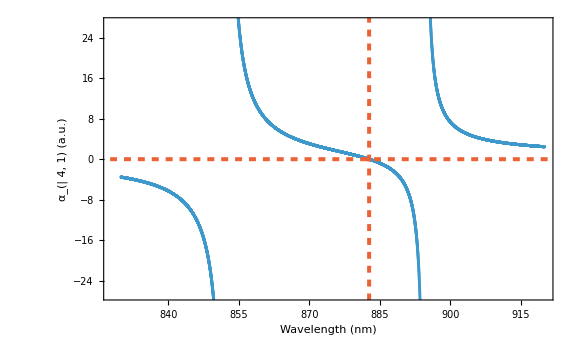

```mathematica
Show[p1,
Frame->True,
 Axes->False, FrameLabel->{Style["Wavelength (nm)",FontSize->22],
Style["α_(| 4,  1) (a.u.)",FontSize->22,FontFamily->"Helvetica"]},
FrameTicksStyle->Directive[18],ImageSize->Large,
FrameStyle->Thick,
Epilog->{Directive[lineStyle],{line2,Hline}}
]
```

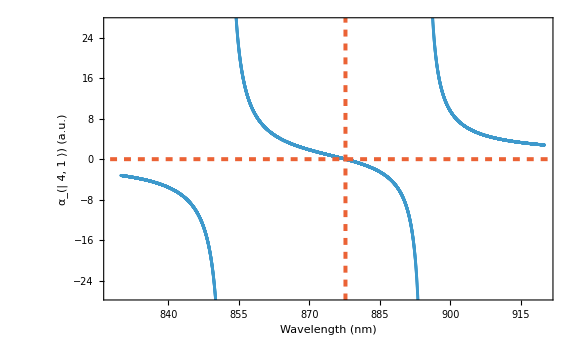

```mathematica
Show[p2,
Frame->True,
 Axes->False, FrameLabel->{Style["Wavelength (nm)",FontSize->22],
Style["α_(| 4,  1  :27e9) (a.u.)",FontSize->22,FontFamily->"Helvetica"]},
FrameTicksStyle->Directive[18],ImageSize->Large,
FrameStyle->Thick,
Epilog->{Directive[lineStyle],{line1,Hline}}
]
```